```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
DefineTensorShortcuts[{{η,v,D,F,Λ,H,R,τ,μ,u,Y,Γ},1},
{{m,G},2},
{{σ,ξ},3}
]
AddBaseIndex[{dotted,{1,2}}]
AddBaseIndex[{undotted,{1,2}}]
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}}}

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}},{undotted,{1,2}}}

Lecture 2010.10.08

T_μν^μν→-ρ g_μν^μν+(p+ρ) u_μ^μ u_ν^ν

{H^2→(8 G π ρ)/3-k/a[t]^2,H→(UnderBar[∂]_t[a])/a}

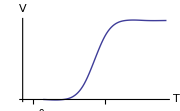
Examine radiation dominate era from 1 MeV to present (10^-4eV).  Starting T at the weak scale (v_0==VEV[Ele.Weak]) assuming Standard Model(SM) particles in contact with thermal bath at T>v_0.
-Graphics-
Possible reactions with thermal bath particles {b_i^i}⇄X
{b_i^i,b_j^j}→scattering→{X,b_k^k}
{b_i^i}→decay→{X,b_k^k}
Impose constraints: Γ[X prod]≫Γ[expand universe]
→ Life time relationships: τ[X prod]≪t_0[age of universe] which can be inferred from H→(UnderBar[∂]_t[a])/a and for any a[t]→t^n ⇒ H→n/t
for any such a[t] the age of the universe is proportional to the inverse of the Hubble parameter.

```mathematica
Get[StringReplace[SaveFile,{"10.08"->"10.04"}]]
Get[StringReplace[SaveFile,{"10.08"->"10.06"}]]
PR1["Examine radiation dominate era from 1 MeV to present (10^-4eV).  Starting T at the weak scale (v_0==VEV[Ele.Weak]) assuming Standard Model(SM) particles in contact with thermal bath at T>v_0.",
NL,
Graphics[
ListPlot[{{0,0,2,8,10,10,10}},Joined->True,InterpolationOrder->3,AxesLabel->{T,V},AxesOrigin->{0,0},Ticks->{{{.5,"m=0",{0,.0}},
{1.2,"",{.03,.06}},
{2.5,"<gain m>",{.0,.0}},
{4,"v_0",{.5,.06}},
{7,"T_0",{.5,.06}}},None},ImageSize->Small]
],
NL,"Possible reactions with thermal bath particles ",{bd[i]}⇄X,
NL,Column[
{{bd[i],bd[j]}->"scattering"->{X,bd[k]},{bd[i]}->"decay"->{X,bd[k]}}
],
NL,"Impose constraints: ",
Γ["X prod"]≫Γ["expand universe"],Yield,
"Life time relationships: ",
τ["X prod"]≪Subscript[t, 0]["age of universe"],
" which can be inferred from ",
tmp=tmpH0,
tmp=tmp/.xPartialD->xD/.a->a[t]/.xD->xD;" and for any ",
sub=a[t]->t^n,imply,
tmp=tmp/.sub/.xD->D,
NL,"for any such a[t] the age of the universe is proportional to the inverse of the Hubble parameter. "
];
```

```mathematica
PR1["Scattering rate for the production of X from the scattering of bath particles {b} is  ",
subΓ=Subscript[Γ, scat[X]]->Subscript[BraKet[σ. v], scat[X]] Subscript[n, b]," where n_b is the density of bath particles.  This rate comes from the production rate of X: ",xPartialD[Subscript[n, X],t]->Subscript[n, b[i]] Subscript[n, b[j]] Subscript[BraKet[σ.v], scat[bb]],
NL,"In the SM {q,u,d,l,e,h} all cary hypercharge so the relevant reactions are: 
{qlh,qlh}(g')⟶  B  ⟶(q'){qlh,qlh}
{qlh,qlh}(g) ⟶  W  ⟶ (q){qlh,qlh}
{qud,qud}(g_3)⟶gluon⟶(q_3){qud,qud}
The coupling constants {g',g,g_3}∼{1/3,2/3,1} are roughly comparable.  So we can approximate ",BraKet[σ.v]∼g^4/T^2," since T is the only available mass scale.  So, ",
sub1=n BraKet[σ.v]∼g^4 T ,
NL,
"From ",tmp=Map[√#&,tmpH]/.k->0//PowerExpand;tmp=tmp/.(tmpρrad/.Subscript[ρ, _][_]->ρ)//PowerExpand,yield,
sub2=tmp/.RuleX1[MassUnits[[2]],G][[1]]//PowerExpand,
NL,"For thermal equilibrium require: ",
tmp=n BraKet[σ.v]≫H,yield,
tmp=tmp/.Apply[Rule,sub1],yield,
tmp=tmp/.sub2,yield,
Solve4Pattern[Apply[Equal,tmp],T][[2,1]]/.Rule->LessLess,
NL,"The right hand side could be as low as 10^15 GeV."
];
```

Scattering rate for the production of X from the scattering of bath particles {b} is  Γ_scat[X]→n_b ⟨σ.v⟩_scat[X] where n_b is the density of bath particles.  This rate comes from the production rate of X: UnderBar[∂]_t[n_X]→n_b[i] n_b[j] ⟨σ.v⟩_scat[bb]
In the SM {q,u,d,l,e,h} all cary hypercharge so the relevant reactions are: 
{qlh,qlh}(g')⟶  B  ⟶(q'){qlh,qlh}
{qlh,qlh}(g) ⟶  W  ⟶ (q){qlh,qlh}
{qud,qud}(g_3)⟶gluon⟶(q_3){qud,qud}
The coupling constants {g',g,g_3}∼{1/3,2/3,1} are roughly comparable.  So we can approximate ⟨σ.v⟩∼g^4/T^2 since T is the only available mass scale.  So, n ⟨σ.v⟩∼g^4 T
From H→(2 √G π^(3/2) T^2 √(g_★))/(3 √5) ⟶ H→(2 π^(3/2) T^2 √(g_★))/(3 √5 m_planck)
For thermal equilibrium require: n ⟨σ.v⟩≫H ⟶ g^4 T≫H ⟶ g^4 T≫(2 π^(3/2) T^2 √(g_★))/(3 √5 m_planck) ⟶ T≪(3 √5 g^4 m_planck)/(2 π^(3/2) √(g_★))
The right hand side could be as low as 10^15 GeV.

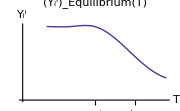
Examine particle decouplings.
For μ_i^i→0 (equal density of particles and anti-particles) and from n_i^i[T]→g_i^i/(2 π^2).∫_En [√(En^2+(m_i^i)^2).En/(ⅇ^((En+μ_i^i)/(k T))±1)]
→ The number density for species {i} for {m>>T, M<<T} ⟶ {n_i^i→(ⅇ^(-m_i^i/T) g_i^i (T m_i^i)^(3/2))/(2 √2 π^(3/2)),n_i^i→(T^3 g_i^i)/π^2}
Define temperature at decoupling for particle {i}, T_decouple[i], as Γ_processChangeNumber[i][T_decouple[i]]==H[T_decouple[i]][Production+ThermalBath]
There are 3 modes of decoupling->
{ShortLived, LongLived->{Relativistic, NonRelativitic}}

The ShortLived decoupling include particles where the life time is less than the age of universe corresponding to temperature at mass of particle[i]: τ_i^i<t[T==n_i^i] which includes {W,Z,t,h,b,c,μ,τ}-Graphics-

```mathematica
PR1["Examine particle decouplings.
For ",μd[i]->0," (equal density of particles and anti-particles) and from ",tmpni,Yield,
"The number density for species {i} for {m>>T, M<<T}",yield,
 Donaldson36={nd[i]->gd[i] ((md[i]T)/(2π))^(3/2)Exp[-md[i]/T],nd[i]->gd[i](T^3/π^2)},
NL,"Define temperature at decoupling for particle {i}, T_decouple[i], as ",
Subscript[Γ, processChangeNumber[i]][Subscript[T, decouple[i]]]==H[Subscript[T, decouple[i]]][Production+ThermalBath],
NL,"There are 3 modes of decoupling->
{ShortLived, LongLived->{Relativistic, NonRelativitic}}

The ShortLived decoupling include particles where the life time is less than the age of universe corresponding to temperature at mass of particle[i]: ",
τd[i]<t[T==nd[i]]," which includes {W,Z,t,h,b,c,μ,τ}",
Graphics[
ListPlot[{{10,10,10,8,5,3}},Joined->True,InterpolationOrder->3,AxesLabel->{T,Yd[i]},AxesOrigin->{0,0},Ticks->{{{3,md[i],{.6,.0}},
{4.7,"<gain m>",{.0,.0}}
},None},PlotLabel->Subscript[Yd[i], Equilibrium][T],ImageSize->Small]
]
 ]
```

```mathematica
PR1["Check ShortLived definition for a few species.
e.g. W-boson: ",Yield,
Γ∼g^2/(8π)Subscript[M, W]->1 [GeV],imply,τd[W]∼HoldForm[10^-24][s],and,
"age of universe at T[mass] ",t[sec]∼(Mev/T)^2->HoldForm[(10^-10)[s]],imply,"ShortLived",
NL,"e.g. μ: ",τd[μ]∼HoldForm[(10^-6)[s]],and,
"age of universe T[mass] ",t[sec]∼(Mev/(T->100[Mev]))^2->HoldForm[(10^-4)[s]],imply,"ShortLived",

NL,"ShortLived particle number ⟶0 exponentially.",
CG["Dodelson uses "],dodelson330=t->132(((.1[MeV])/T)^2)[s],
CG[" for age of universe[T]."]
];
```

Check ShortLived definition for a few species.
e.g. W-boson: 
→ Γ∼(g^2 M_W)/(8 π)→1[GeV] ⇒ τ_W^W∼1/10^24[s] and age of universe at T[mass] t[sec]∼Mev^2/T^2→1/10^10[s] ⇒ ShortLived
e.g. μ: τ_μ^μ∼1/10^6[s] and age of universe T[mass] t[sec]∼Mev^2/(T→100[Mev])^2→1/10^4[s] ⇒ ShortLived
ShortLived particle number ⟶0 exponentially.Dodelson uses t→132 (0.1[MeV])^2/T^2[s] for age of universe[T].

```mathematica
PR1["Boltzmann equation for number density ",
tmpdn=
xPartialD[nd[i],t]+3(ȧ)/a nd[i]==-Γd[i](nd[i][decay]-Subscript[nd[i], equil][production]),
NL,CG["Dodelson's Boltzmann equation for interaction {1,2}->{3,4} is "],
dodelson39=xPartialD[a[t]^3 nd[1][t],t]/a[t]^3==nd[1][0]nd[2][0]BraKet[σ.v]((nd[3][t]nd[4][t])/(nd[3][0]nd[4][0])-(nd[1][t]nd[2][t])/(nd[1][0]nd[2][0]))
]
```

Boltzmann equation for number density (3 ȧ n_i^i)/a+UnderBar[∂]_t[n_i^i]==-Γ_i^i (-(n_i^i)_equil[production]+n_i^i[decay])
Dodelson's Boltzmann equation for interaction {1,2}->{3,4} is (UnderBar[∂]_t[a[t]^3 n_1^1[t]])/a[t]^3==⟨σ.v⟩ n_1^1[0] n_2^2[0] (-(n_1^1[t] n_2^2[t])/(n_1^1[0] n_2^2[0])+(n_3^3[t] n_4^4[t])/(n_3^3[0] n_4^4[0]))

```mathematica
PR1["Check ShortLived definition for a few species.
e.g. strange-quark{m_s∼100 MeV}: ",yield,
Subscript[τ, s]∼HoldForm[(10^-6)[s]],
NL,"But there are not many particles to decay to: {s,u,d,g}->{π,K,p,n,Λ,η}.  e.g.,{s}->{u,{e,ν̄}} and {s}-{νd[μ],{W->{e,(ν̄)_e}}.
Is there QCD phase transition ",t<Subscript[τ, QCD][PhaseTransition]∼HoldForm[(10^-4)[s]],
NL,"{p,n,e,νd[i],γ} remain and are LongLived and relativistic decouple only after T< M_{w, Z} mass.  
Thermal reactions {d,u}-{W}->{u,l} and {e,l}-{Z}->{ν,ν}.
While in thermal equilibrium ",BraKet[σ.v]∼Subscript[G, F]^2 T^2,yield,
tmpG=Γd[thermal[ν]]->T^3{nd[i]}.(Subscript[G, F]^2).T^2->Subscript[G, F]^2 T^5,
NL,tmpH=H∼T^2/Subscript[M, p1],
NL,"Decoupling temperature ",Subscript[T, ν]," by solving ",
tmpH==tmpG/.T->Subscript[T, ν],yield,tmp=tmpH[[2]]==tmpG[[2,2]]/.T->Subscript[T, ν],yield,
tmp=Map[#/Subscript[T, ν]^2&,tmp],yield,
Solve4Pattern[tmp,Subscript[T, ν]^3][[1]]
]
```

Check ShortLived definition for a few species.
e.g. strange-quark{m_s∼100 MeV}:  ⟶ τ_s∼1/10^6[s]
But there are not many particles to decay to: {s,u,d,g}->{π,K,p,n,Λ,η}.  e.g.,{s}->{u,{e,ν̄}} and {s}-{νd[μ],{W->{e,(ν̄)_e}}.
Is there QCD phase transition (t<τ_QCD[PhaseTransition])∼1/10^4[s]
{p,n,e,νd[i],γ} remain and are LongLived and relativistic decouple only after T< M_{w, Z} mass.  
Thermal reactions {d,u}-{W}->{u,l} and {e,l}-{Z}->{ν,ν}.
While in thermal equilibrium ⟨σ.v⟩∼T^2 G_F^2 ⟶ Γ_thermal[ν]^thermal[ν]→T^3 {n_i^i}.G_F^2.T^2→T^5 G_F^2
H∼T^2/M_p1
Decoupling temperature T_ν by solving (H∼T_ν^2/M_p1)==(Γ_thermal[ν]^thermal[ν]→{n_i^i}.G_F^2.T_ν^2 T_ν^3→G_F^2 T_ν^5) ⟶ T_ν^2/M_p1==G_F^2 T_ν^5 ⟶ 1/M_p1==G_F^2 T_ν^3 ⟶ {T_ν^3→1/(G_F^2 M_p1)}

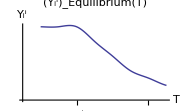
LongLived States.  Non-relativistic decoupling follow Boltzmann process.-Graphics-
Consider reactions affecting particle density X with thermal bath {X,b}→{anything} and {X,X̄}→{anything}(3 ȧ n_i^i)/a+UnderBar[∂]_t[n_i^i]==-Γ_i^i (-(n_i^i)_equil[production]+n_i^i[decay]) ⇒ (3 ȧ n_X^X[t])/a+(n_X^X)'[t]→-⟨σ.v⟩ (-n_b^b[eq] n_X^X[eq]+n_b^b[t] n_X^X[t])

```mathematica
PR1["LongLived States.  Non-relativistic decoupling follow Boltzmann process.",
Graphics[
ListPlot[{{10,10,10,8,6,4,3,2}},Joined->True,InterpolationOrder->3,AxesLabel->{T,Yd[i]},AxesOrigin->{0,0},Ticks->{{{3,md[i],{.6,.03}},
{4.7,Style["<Boltzmann>",Tiny],{.0,.0}},
{7,Style[Subscript[T, decouple],Tiny],{.6,.03}}
},None},PlotLabel->Subscript[Yd[i], Equilibrium][T],ImageSize->Small]
],
NL,"Consider reactions affecting particle density X with thermal bath ",
{X,b}->{anything},and,{X,X̄}->{anything},
tmpdn,imply,
tmpdn1=(tmpdn[[1]]/.nd[i_]->nd[X][t]/.xPartialD->xD/.xD->D)->-BraKet[σ.v](nd[X][t]nd[b][t]-nd[X][eq]nd[b][eq])
];
```

```mathematica
PR1[
NL,"Apply to {p,n,e} of standard model to determine FreezeOut, e.g., consider processes {e,ē}->{γ,γ} or {p,p̄}->{π,π}.
FreezeOut determined by solutions of above rate equation for ", nd[X][t],
NL,"From the definition ",
tmpY0=Y[t]->n[t]/s[t],yield,
tmpy=Map[D[#,t]&,tmpY0],NL,and,
tmps1=tmpss/.s->s[t]/.a->a[t],yield,
tmp=Map[D[#,t]&,tmps1]/.RuleX[tmps1,S],yield,
tmpy=tmpy/.tmp,Imply,
suby=Map[# s[t]&,tmpy]/.a[t]->a/.a'[t]->ȧ/.n->nd[X]/.Y->Yd[X]//Simplify//Reverse,
NL,"So ",
tmp=tmpdn1/.xPartialD->xD/.xD->D,yield,
tmp=tmp/.suby/.nd[a_][b_]->s[t]Yd[a][b]//Simplify,
NL,"with ",tmp1=tmpss/.tmps/.s->s[t],
NL,Framed[
tmpY=Map[#/s[t]&,tmp]/.tmp1
]
];
```

Apply to {p,n,e} of standard model to determine FreezeOut, e.g., consider processes {e,ē}->{γ,γ} or {p,p̄}->{π,π}.
FreezeOut determined by solutions of above rate equation for n_X^X[t]
From the definition Y[t]→n[t]/s[t] ⟶ Y'[t]→n'[t]/s[t]-(n[t] s'[t])/s[t]^2
 and s[t]→S/a[t]^3 ⟶ s'[t]→-(3 s[t] a'[t])/a[t] ⟶ Y'[t]→(3 n[t] a'[t])/(a[t] s[t])+n'[t]/s[t]
⇒ (3 ȧ n_X^X[t])/a+(n_X^X)'[t]→s[t] (Y_X^X)'[t]
So (3 ȧ n_X^X[t])/a+(n_X^X)'[t]→-⟨σ.v⟩ (-n_b^b[eq] n_X^X[eq]+n_b^b[t] n_X^X[t]) ⟶ s[t] (Y_X^X)'[t]→⟨σ.v⟩ s[t]^2 (Y_b^b[eq] Y_X^X[eq]-Y_b^b[t] Y_X^X[t])
with s[t]→2/45 π^2 T^3 g_★
(Y_X^X)'[t]→2/45 π^2 T^3 ⟨σ.v⟩ g_★ (Y_b^b[eq] Y_X^X[eq]-Y_b^b[t] Y_X^X[t])

```mathematica
PR1["Compute D[Y[T],T] given Y[t] -> Y[T] ",Yield,
tmp=Y[t]->Y[T[t]],Yield,
tmpdt=Map[D[#,t]&,tmp],
NL,"Since ",
tmp=a[t]T[t]==Constant,Yield,
tmp=Map[D[#,t]&,tmp],yield,
sub=Solve4Pattern[tmp,D[T[t],t]]//Flatten,imply,
tmp=tmpdt/.sub,
NL,"Hubble parameter definition ",
tmp2=tmpH0/.a->a[t]/.xPartialD->xD/.xD->D;
tmp2=Solve4Pattern[tmp2,D[a[t],t]]//Flatten,imply,
Framed[
subY=tmp/.tmp2/.T[t]->T]
];
```

Compute D[Y[T],T] given Y[t] -> Y[T] 
→ Y[t]→Y[T[t]]
→ Y'[t]→T'[t] Y'[T[t]]
Since a[t] T[t]==Constant
→ T[t] a'[t]+a[t] T'[t]==0 ⟶ {T'[t]→-(T[t] a'[t])/a[t]} ⇒ Y'[t]→-(T[t] a'[t] Y'[T[t]])/a[t]
Hubble parameter definition {a'[t]→H a[t]} ⇒ Y'[t]→-H T Y'[T]

```mathematica
PR1["We can transform {t->T} the equation for ",First[tmpY],Yield,
tmp=tmpY/.(subY/.Y->Yd[X])/.t->T,Yield,
tmp=Solve4Pattern[tmp,D[Yd[X][T],T]]//Flatten//First,Yield,
tmp=Map[T #/Yd[X][T]&,tmp]/.g_★->g_★Yd[bx][T];
tmpYT=MapAt[#/Yd[b][T]&,tmp,2],
NL,"Since ",
sub=Yd[bx][T]->nd[bx][T]/s,yield,
sub=sub/.tmpss/.tmps,and,subΓ,Imply,
tmp=tmpYT/.sub/.bx->b/.Reverse[subΓ/.Subscript[a_, scat[X]]->a/.Subscript[n, b]->nd[b][T]],
NL,"Define FreezeOut temperature ",Subscript[T, f][Γ==H]
];
```

We can transform {t->T} the equation for (Y_X^X)'[t]
→ -H T (Y_X^X)'[T]→2/45 π^2 T^3 ⟨σ.v⟩ g_★ (Y_b^b[eq] Y_X^X[eq]-Y_b^b[T] Y_X^X[T])
→ (Y_X^X)'[T]→-(2 π^2 T^2 ⟨σ.v⟩ g_★ (Y_b^b[eq] Y_X^X[eq]-Y_b^b[T] Y_X^X[T]))/(45 H)
→ (T (Y_X^X)'[T])/Y_X^X[T]→-(2 π^2 T^3 ⟨σ.v⟩ g_★ Y_bx^bx[T] (Y_b^b[eq] Y_X^X[eq]-Y_b^b[T] Y_X^X[T]))/(45 H Y_b^b[T] Y_X^X[T])
Since Y_bx^bx[T]→n_bx^bx[T]/s ⟶ Y_bx^bx[T]→(45 n_bx^bx[T])/(2 π^2 T^3 g_★) and Γ_scat[X]→n_b ⟨σ.v⟩_scat[X]
⇒ (T (Y_X^X)'[T])/Y_X^X[T]→-(Γ (Y_b^b[eq] Y_X^X[eq]-Y_b^b[T] Y_X^X[T]))/(H Y_b^b[T] Y_X^X[T])
Define FreezeOut temperature T_f[Γ==H]

```mathematica
PR1["Estimate FreezeOut abundance from the number density for relativistic particles (Dodelson.3.6) is ",
tmp=Donaldson36//First;
subn=tmp/.{md[i]->md[X],gd[i]->gd[X],T->Subscript[T, f],i->X},
NL,"The condition for FreezeOut",imply,
tmp=subΓ[[2]]==tmpH[[2]]/.Subscript[BraKet[a_], _]->BraKet[a]/.T->Subscript[T, f],yield,
tmpnf=Solve[tmp,Subscript[n, b]]//Flatten,Yield,
tmpnf1=tmpnf[[1,2]]==subn[[2]],yield,
tmp=Map[#/(Subscript[T, f]^2 md[X])&,tmpnf1]//PowerExpand,
NL,"Defining: ",subX=md[X]/Subscript[T, f]->Subscript[X, f],Imply,tmp=tmp/.RuleX[subX,md[X]]//PowerExpand,Yield,
tmp=MapAt[#/.RuleX[subX,Subscript[X, f]]&,tmp,1],Yield,
Framed[
tmpeX=Solve4Pattern[tmp,Exp[-Subscript[X, f]]]//PowerExpand//Flatten//First]
];
```

Estimate FreezeOut abundance from the number density for relativistic particles (Dodelson.3.6) is n_X^X→(ⅇ^(-m_X^X/T_f) g_X^X (T_f m_X^X)^(3/2))/(2 √2 π^(3/2))
The condition for FreezeOut ⇒ ⟨σ.v⟩ n_b==T_f^2/M_p1 ⟶ {n_b→T_f^2/(⟨σ.v⟩ M_p1)}
→ T_f^2/(⟨σ.v⟩ M_p1)==(ⅇ^(-m_X^X/T_f) g_X^X (T_f m_X^X)^(3/2))/(2 √2 π^(3/2)) ⟶ 1/(⟨σ.v⟩ M_p1 m_X^X)==(ⅇ^(-m_X^X/T_f) g_X^X (m_X^X)^(1/2))/(2 √2 π^(3/2) √T_f)
Defining: m_X^X/T_f→X_f
⇒ 1/(⟨σ.v⟩ M_p1 T_f X_f)==(ⅇ^-X_f √X_f g_X^X)/(2 √2 π^(3/2))
→ 1/(⟨σ.v⟩ M_p1 m_X^X)==(ⅇ^-X_f √X_f g_X^X)/(2 √2 π^(3/2))
→ ⅇ^-X_f→(2 √2 π^(3/2))/(⟨σ.v⟩ M_p1 √X_f g_X^X m_X^X)

```mathematica
PR1["From: ",subn,Yield,
tmp=subn/.RuleX[subX,md[X]]/.RuleX[subX,Subscript[T, f]]//PowerExpand,Yield,
tmp=tmp/.tmpeX,Yield,
tmp=Map[#/s&,tmp],yield,
tmp[[1]]=Yd[f];
tmp,
NL,"We use the Eliminate[] function and Solve[] for Yd[f] with:",Yield,
tmp={tmp,tmpss,(tmps/.T->Subscript[T, f]),subX}/.Rule->Equal,Yield,
tmp=Refine[Eliminate[tmp,{s,S,Subscript[T, f]}],a≠0&&BraKet[_]≠0&&Subscript[M, _]≠0&&Subscript[X, f]≠0],Yield,
Framed[
tmpYf=Solve[tmp,Yd[f]]//Flatten//First]
];
```

From: n_X^X→(ⅇ^(-m_X^X/T_f) g_X^X (T_f m_X^X)^(3/2))/(2 √2 π^(3/2))
→ n_X^X→(ⅇ^-X_f g_X^X (m_X^X)^3)/(2 √2 π^(3/2) X_f^(3/2))
→ n_X^X→((m_X^X)^2)/(⟨σ.v⟩ M_p1 X_f^2)
→ n_X^X/s→((m_X^X)^2)/(s ⟨σ.v⟩ M_p1 X_f^2) ⟶ Y_f^f→((m_X^X)^2)/(s ⟨σ.v⟩ M_p1 X_f^2)
We use the Eliminate[] function and Solve[] for Yd[f] with:
→ {Y_f^f==((m_X^X)^2)/(s ⟨σ.v⟩ M_p1 X_f^2),s==S/a^3,S==2/45 a^3 π^2 g_★ T_f^3,m_X^X/T_f==X_f}
→ 2 π^2 g_★ m_X^X Y_f^f==(45 X_f)/(⟨σ.v⟩ M_p1)
→ Y_f^f→(45 X_f)/(2 π^2 ⟨σ.v⟩ g_★ M_p1 m_X^X)

```mathematica
Save[SaveFile,{tmpY0,tmpYf,subX,subn,dodelson39,dodelson330}]
```